```mathematica
Sum[(-1)^(k)*coeff[2m+1-k,k]/(4(2m+1-k)(2m+1-k-1/2)),{k,0,m}]
```

-[m]/2

```mathematica
Sum[(-1)^(k)*coeff[2m-k,k]/(4(2m-k)(2m-k-1/2)),{k,0,m}]
```

(Binomial[4 m,-1+2 m] HypergeometricPFQ[{1/2-m,1-m,-2 m},{1-2 m,3/2-2 m},1])/(8 m^2 (-1+4 m))

```mathematica
RSolve[{(-1-3 n-2 n^2) y[n]+(2+n) (3+2 n) y[1+n]==0,y[1]==-1/6},y[n],n]
```

{{y[n]→1/(1+3 n+2 n^2)}}

```mathematica
fun[x_]:=2/(1+x)
```

```mathematica
coeff[n_,k_]:=Binomial[2n,n-k-1]*Binomial[n+k-1,k]/(n)
```

```mathematica
Sum[(-1)^(k)*fun[x]^(-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,∞}]
```

(Binomial[2 m,-1+m] HypergeometricPFQ[{1/2-m/2,1-m/2,-m},{1-m,3/2-m},(1+x)/2])/(2 m^2 (-1+2 m))

```mathematica
TableForm[Table[Apart[m(m+1)Sum[(-1)^(k)*fun[x]^(-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,Floor[m/2]}]],{m,1,10}]]
```

1
1
3/2-x/2
3-2 x
7-(13 x)/2+x^2/2
71/4-(41 x)/2+(15 x^2)/4
379/8-(519 x)/8+(153 x^2)/8-(5 x^3)/8
131-207 x+84 x^2-7 x^3
2975/8-(1331 x)/2+(1371 x^2)/4-49 x^3+(7 x^4)/8
8619/8-2153 x+1341 x^2-(555 x^3)/2+(105 x^4)/8

```mathematica
TableForm[Table[Table[coeff[n,k],{k,0,n-1}],{n,1,10}]]
```

1 |  |  |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  |  |  | 
5 | 6 | 2 |  |  |  |  |  |  | 
14 | 28 | 20 | 5 |  |  |  |  |  | 
42 | 120 | 135 | 70 | 14 |  |  |  |  | 
132 | 495 | 770 | 616 | 252 | 42 |  |  |  | 
429 | 2002 | 4004 | 4368 | 2730 | 924 | 132 |  |  | 
1430 | 8008 | 19656 | 27300 | 23100 | 11880 | 3432 | 429 |  | 
4862 | 31824 | 92820 | 157080 | 168300 | 116688 | 51051 | 12870 | 1430 | 
16796 | 125970 | 426360 | 852720 | 1108536 | 969969 | 570570 | 217360 | 48620 | 4862

```mathematica
Series[Tanh[ArcSin[Tan[x]]],{x,0,12}]
```

x+x^3/6+x^5/120+x^7/5040+(7681 x^9)/362880+(1689601 x^11)/39916800+O[x]^13

```mathematica
aa:={1,-1/3,2/15,-17/315,62/2835,-1382/155925}
```

```mathematica
Table[aa[[n]]*n!,{n,1,Length[aa]}]
```

{1,-2/3,4/5,-136/105,496/189,-22112/3465}

```mathematica
mysum[m_]:=Sum[(-1)^(k)*G[x]^(-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,Floor[m/2]}]
```

```mathematica
Sum[(-1)^(k)*fun[x]^(m-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,∞}]
```

(2^(-1+m) (1/(1+x))^m Binomial[2 m,-1+m] HypergeometricPFQ[{1/2-m/2,1-m/2,-m},{1-m,3/2-m},(1+x)/2])/(m^2 (-1+2 m))

```mathematica
FullSimplify[Sum[(-1)^(k)*G[x]^(2m+1-k)*coeff[2m+1-k,k]/(4(2m+1-k)(2m-k+1/2)),{k,0,m}]]
```

2^(-1+2 m) (1/(1+x))^(1+2 m) [m]

```mathematica
Plot[Table[Table[Abs[2^m (1/(1+x))^m-Sum[(-1)^(k)*(fun[x])^(m-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,Floor[m/2]}]],{x,1,50}],{m,1,10}],PlotLegends->Automatic, PlotStyle->{Thin,PointSize[Large]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

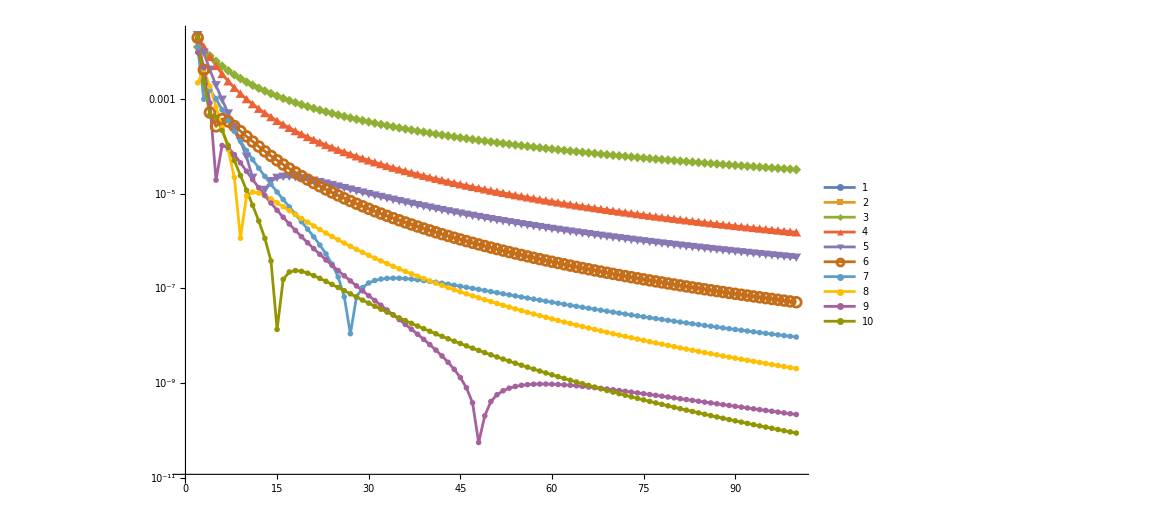

```mathematica
ListLogPlot[Table[Table[Abs[(fun[x])^m/(m(m+1))-(2^(-1+m) (1/(1+x))^m Binomial[2 m,-1+m] HypergeometricPFQ[{1/2-m/2,1-m/2,-m},{1-m,3/2-m},(1+x)/2])/(m^2 (-1+2 m))],{x,1,100}],{m,1,10}],PlotLegends->Automatic,Joined->True,PlotMarkers->{Automatic,10}]
```

```mathematica
D[HypergeometricPFQ[{1/2-m/2,1-m/2,-m},{1-m,3/2-m},(1+x)/2],{x,m}]
```

2^-m m! [m]

```mathematica
MonomialList[(f/2+
(8/3*f^2-2*f^3)/12+
(11f^3-24f^4+16f^5)/30+
(908/15*f^4-1296/5*f^5+27320/63*f^6-272*f^7)/56
)+0*(908/15*f^4-1296/5*f^5+27320/63*f^6-272*f^7)*Sum[1/(2m(2m-1)), {m,5,∞}],f]
```

{-(34 f^7)/7,(3415 f^6)/441,-(86 f^5)/21,(59 f^4)/210,f^3/5,(2 f^2)/9,f/2}

```mathematica
Z6:=S6;
Z24:=S24-Z6;
Z222:=S222-3*Z24;
```

```mathematica
MonomialList[15Z222+15Z24+Z6]
```

{15 S222,-30 S24,31 S6}

```mathematica
Integrate[s^(2n)*Exp[-t/2*s],{s,0,∞},Assumptions->Element[t,Reals]&&t>0&&n>0&&Element[n,Integers]]
```

2^(1+2 n) t^(-1-2 n) Gamma[1+2 n]

```mathematica
{Factor[Integrate[Integrate[(1)!*k/t^(2+k),t],t]],
Factor[Integrate[Integrate[Integrate[Integrate[(1)!*k/t^(4+k),t],t],t],t]],
Factor[Integrate[Integrate[Integrate[Integrate[Integrate[Integrate[(1)!*k/t^(6+k),t],t],t],t],t],t]]
}
```

{t^-k/(1+k),t^-k/((1+k) (2+k) (3+k)),t^-k/((1+k) (2+k) (3+k) (4+k) (5+k))}

```mathematica
Table[{FunctionExpand[Binomial[2n+k-1,2n]^(-1)*k],FunctionExpand[(Gamma[1+k] Gamma[2 n+1])/Gamma[k+2 n]]},{n,1,3}]
```

{{2/(1+k),2/(1+k)},{24/((1+k) (2+k) (3+k)),24/((1+k) (2+k) (3+k))},{720/((1+k) (2+k) (3+k) (4+k) (5+k)),720/((1+k) (2+k) (3+k) (4+k) (5+k))}}

```mathematica
F[a_,b_,c_,n_,k_]:=(k-1)(k-2)a!b!c!+(k-1)*(Factorial[a]*Factorial[2*n-a]+Factorial[b]*Factorial[2*n-b]+Factorial[c]*Factorial[2*n-c])+Factorial[2*n]
```

```mathematica
Factor[G[2,2,2,3,k]]
```

8 (74+15 k+k^2)

```mathematica
G[a_,b_,c_,n_,k_]:=Gamma[a+1]*Gamma[b+1]*Gamma[c+1]*k^2+Gamma[2n+1]*(Binomial[2n,a]^(-1)+Binomial[2n,b]^(-1)+Binomial[2n,c]^(-1)-3*Gamma[a+1]*Gamma[b+1]*Gamma[c+1]/Gamma[2n+1])*k-Gamma[2n+1]*(Binomial[2n,a]^(-1)+Binomial[2n,b]^(-1)+Binomial[2n,c]^(-1)-2*Gamma[a+1]*Gamma[b+1]*Gamma[c+1]/Gamma[2n+1]-1)
```

```mathematica
Gone[n_,x_]:=Gamma[x+1]*Gamma[n+1]/Gamma[n+x]
```

```mathematica
Gtwo[n_,m_,x_]:=Gamma[x+1]/Gamma[n+m+x]*(Gamma[n+1]*Gamma[m+1]*x+Gamma[n+m+1]-Gamma[n+1]*Gamma[m+1])
```

```mathematica
Gthree[a_,b_,c_,x_]:=Gamma[x+1]/Gamma[a+b+c+x]*(Gamma[a+1]*Gamma[b+1]*Gamma[c+1]*x^2+Gamma[a+b+c+1]*(Binomial[a+b+c,a]^(-1)+Binomial[a+b+c,b]^(-1)+Binomial[a+b+c,c]^(-1)-3*Gamma[a+1]*Gamma[b+1]*Gamma[c+1]/Gamma[a+b+c+1])*x-Gamma[a+b+c+1]*(Binomial[a+b+c,a]^(-1)+Binomial[a+b+c,b]^(-1)+Binomial[a+b+c,c]^(-1)-2*Gamma[a+1]*Gamma[b+1]*Gamma[c+1]/Gamma[a+b+c+1]-1))
```

```mathematica
Gfour[x_]:=16(x^3+30x^2+371x+2118)/( (1+x)(2+x)(3+x)(4+x)(5+x)(6+x)(7+x) );FunctionExpand[Gone[2,x]]
```

2/(1+x)

```mathematica
monomials:=MonomialList[f*2/(1+x)/2
+( 2(f^2-f^3)*4(x+5)/((x+1)(x+2)(x+3))+f^3*12/((x+2)(x+3)) )/12
+( (5f^3-12f^4+7f^5)*8(x^2+15x+74)/((x+1)(x+2)(x+3)(x+4)(x+5))+6(f^4-f^5)*24(x+14)/((x+2)(x+3)(x+4)(x+5))+f^5*120/((3+x)(4+x)(5+x)) )/30
+( 14*16(x^3+30x^2+371x+2118)/((x+1)(x+2)(x+3)(x+4)(x+5)(x+6)(x+7))*f^4+rest )/56,f,"NegativeLexicographic"];monomials
```

{rest/56,f/(1+x),f^2 (10/(3 (1+x) (2+x) (3+x))+(2 x)/(3 (1+x) (2+x) (3+x))),f^3 (1/((2+x) (3+x))-10/(3 (1+x) (2+x) (3+x))-(2 x)/(3 (1+x) (2+x) (3+x))+296/(3 (1+x) (2+x) (3+x) (4+x) (5+x))+(20 x)/((1+x) (2+x) (3+x) (4+x) (5+x))+(4 x^2)/(3 (1+x) (2+x) (3+x) (4+x) (5+x))),f^4 (336/(5 (2+x) (3+x) (4+x) (5+x))+(24 x)/(5 (2+x) (3+x) (4+x) (5+x))-1184/(5 (1+x) (2+x) (3+x) (4+x) (5+x))-(48 x)/((1+x) (2+x) (3+x) (4+x) (5+x))-(16 x^2)/(5 (1+x) (2+x) (3+x) (4+x) (5+x))+8472/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))+(1484 x)/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))+(120 x^2)/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))+(4 x^3)/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))),f^5 (4/((3+x) (4+x) (5+x))-336/(5 (2+x) (3+x) (4+x) (5+x))-(24 x)/(5 (2+x) (3+x) (4+x) (5+x))+2072/(15 (1+x) (2+x) (3+x) (4+x) (5+x))+(28 x)/((1+x) (2+x) (3+x) (4+x) (5+x))+(28 x^2)/(15 (1+x) (2+x) (3+x) (4+x) (5+x)))}

```mathematica
TableForm[Table[Factor[FunctionExpand[monomials[[n+1]]n(n+1)]],{n,1,Length[monomials]-1}]]
```

```mathematica
{{(2 f)/(1+x)}, {(4 f^2 (5+x))/((1+x) (2+x) (3+x))}, {(4 f^3 (156+17 x+6 x^2+x^3))/((1+x) (2+x) (3+x) (4+x) (5+x))}, {(16 f^4 (1686+359 x+412 x^2+61 x^3+2 x^4))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))}, {(32 f^5 (74-30 x+x^2))/((1+x) (2+x) (3+x) (4+x) (5+x))}}
```

```mathematica
FunctionExpand[Factor[
105Gfour[x]-420Gthree[2,2,4,x]+140Gtwo[4,4,x]+448Gtwo[2,6,x]-272Gone[8,x]
]]
```

1680/((4+x) (5+x) (6+x) (7+x))

```mathematica
Log[Cosh[0]]
```

0

```mathematica
Apart[(1686+359 x+412 x^2+61 x^3+2 x^4)/(156+17 x+6 x^2+x^3)]
```

49+2 x+(6 (-993-131 x+14 x^2))/(156+17 x+6 x^2+x^3)

```mathematica
FFlist:={f,(8/3f^2-2f^3),(11f^3-24f^4+16f^5),(908/15f^4-1296/5f^5+27320/63f^6-272f^7)}
```

```mathematica
Solve[{1686-78 a-5 b-c==0,359-(17 a)/2-b==0,412-3 a==0}]
```

{{a→412/3,b→-2425/3,c→-14953/3}}

```mathematica
FindSequenceFunction[{112/3,288,944,4600/3,1272,504,72},x]
```

FindSequenceFunction[{112/3,288,944,4600/3,1272,504,72},x]

```mathematica
seq=Table[Expand[FunctionExpand[Binomial[n+k,k]*Factor[k]]],{k,1,8}];
```

```mathematica
GuessPolnomialSequence[seq,n]
```

GuessPolnomialSequence[{1+n,2+3 n+n^2,3+(11 n)/2+3 n^2+n^3/2,4+(25 n)/3+(35 n^2)/6+(5 n^3)/3+n^4/6,5+(137 n)/12+(75 n^2)/8+(85 n^3)/24+(5 n^4)/8+n^5/24,6+(147 n)/10+(203 n^2)/15+(49 n^3)/8+(35 n^4)/24+(7 n^5)/40+n^6/120,7+(363 n)/20+(3283 n^2)/180+(6769 n^3)/720+(49 n^4)/18+(161 n^5)/360+(7 n^6)/180+n^7/720,8+(761 n)/35+(29531 n^2)/1260+(267 n^3)/20+(1069 n^4)/240+(9 n^5)/10+(13 n^6)/120+n^7/140+n^8/5040},n]

```mathematica
f11[x_]:=(16 (1686+359 x+412 x^2+61 x^3+2 x^4))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x));
g11[x_]:=2/(1+x);
```

```mathematica
Series[f11[InverseFunction[g11][y]],{y,0,10}]
```

```mathematica
mono=MonomialList[Normal[Series[f11[x],{x,0,10}]],x,"NegativeLexicographic"];
mono
```

{562/105,-(280879 x)/22050,(188836811 x^2)/9261000,-(103753161499 x^3)/3889620000,(50752666160291 x^4)/1633640400000,-(23208399103573819 x^5)/686128968000000,(10211727152092685171 x^6)/288174166560000000,-(4397350475296366413739 x^7)/121033149955200000000,(1871377029959108868988451 x^8)/50833922981184000000000,-(791383863617424221469639259 x^9)/21350247652097280000000000,(333555612368939009743283682131 x^10)/8967104013880857600000000000}

```mathematica
Table[mono[[n]]*105^n*2^(2n-2),{n,1,Length[mono]}]
```

{562,-561758 x,377673622 x^2,-207506322998 x^3,101505332320582 x^4,-46416798207147638 x^5,20423454304185370342 x^6,-8794700950592732827478 x^7,3742754059918217737976902 x^8,-1582767727234848442939278518 x^9,667111224737878019486567364262 x^10}